```mathematica
SetDirectory["~/Documents/Univ/c++/seminar"];
```

```mathematica
Oscillator=Import["oscillator.dat"];
```

```mathematica
xList=Oscillator.{{1,0},{0,1},{0,0}};
```

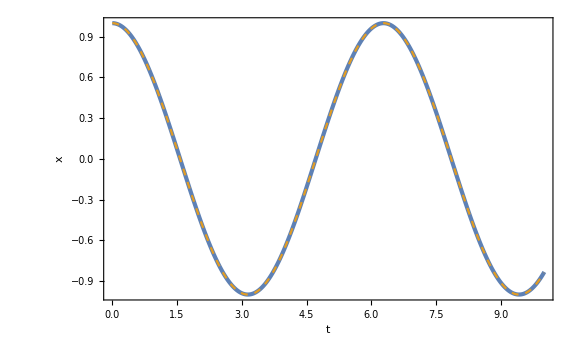

```mathematica
Show[ListPlot[xList,FrameLabel->{t,x},PlotLegends->Placed[LineLegend[{"num"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->20],{0.87,0.8}]],Plot[Cos[t],{t,0,10},PlotStyle->{Color[2],Dashed},PlotLegends->Placed[LineLegend[{"cos t"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->20],{0.87,0.8}]]]
```